### Constants

```mathematica
baseDirectory=ParentDirectory@NotebookDirectory[]
```

/home/christopher/git/ecosystem_dimension_reduction

```mathematica
inputDirectory=FileNameJoin[{baseDirectory,"input_files"}]
```

/home/christopher/git/ecosystem_dimension_reduction/input_files

```mathematica
outputDirectory=FileNameJoin[{baseDirectory,"output_files"}]
```

/home/christopher/git/ecosystem_dimension_reduction/output_files

### Raw data import

```mathematica
rawCSV=Import[FileNameJoin[{outputDirectory,"100000CellSpeciesCounts.csv"}]];
```

### Import cell points

```mathematica
cellPointsRaw=Import[FileNameJoin[{inputDirectory,"100000SpherePoints.csv"}]];
```

```mathematica
cellPoints=GeoPosition[GeoPosition[GeoPositionXYZ[cellPointsRaw,1]][[1,All,;;2]]]
```

GeoPosition[{{-89.5562, 137.508}, {-89.427, -84.9845}, {-89.3221, 52.5233}, {-89.2313, -169.969}, {-89.1502, -32.4612}, {-89.0761, 105.047}, {-89.0076, -117.446}, {-88.9435, 20.0621}, {-88.8831, 157.57}, {-88.8258, -64.9224}, {-88.7711, 72.5854}, <<99983>>, {89.0761, -111.134}, {89.1502, 26.3739}, {89.2313, 163.882}, {89.3221, -58.6105}, {89.427, 78.8972}, {89.5562, -143.595}}]

```mathematica
removeAltitude[gp_]:=GeoPosition[GeoPosition[gp][[1,;;2]]]
```

```mathematica
GeoVoronoi[ps_]:=
Module[{chm,coords,verts},chm=ConvexHullMesh[GeoPositionXYZ[ps][[1]]];
coords=MeshCoordinates[chm];
verts=removeAltitude/@Thread[GeoPositionXYZ[Cross[coords[[#2]]-coords[[#1]],coords[[#3]]-coords[[#1]]]&@@@MeshCells[chm,2][[All,1]]]];
GeoPolygon[verts[[#]]]&/@dual[chm][[2]]]
GeoVoronoi[ps_GeoPosition]:=GeoVoronoi[Thread[ps]]
```

```mathematica
cellPolygons=GeoVoronoi[cellPoints];//EchoTiming
```

32.6243

```mathematica
cellPolygons=;
```

```mathematica
Graphics3D@DualPolyhedron@ConvexHullMesh[SpherePoints[10000]]
```

```mathematica
Graphics3D@dual@ConvexHullMesh[SpherePoints[10000]]
```

#### Fast dual code

```mathematica
sortvertices[coords_,normal_,face_]:=With[{proj=DeleteCases[Orthogonalize[Join[{normal},N@IdentityMatrix[3]]],{0.,0.,0.}][[2;;3]]},SortBy[face,ArcTan@@(proj.coords[[#]])&]];

iDual[coords_?MatrixQ,faces:{{__Integer}..}]:=With[{nvertices=Max@faces,nfaces=Length@faces},With[{mat=SparseArray@Flatten@Table[{v,f}->1,{f,nfaces},{v,faces[[f]]}],dualcoords=Mean[coords[[#]]]&/@faces},With[{dualfaces=mat["AdjacencyLists"]},Polyhedron[dualcoords,Table[sortvertices[dualcoords,coords[[v]],dualfaces[[v]]],{v,Length@dualfaces}]]]]];

(*user-level functions*)
dual[polyhedron:Graphics3D@GraphicsComplex[coords_,Polygon[faces_]]]:=iDual[coords,faces];
dual[polyhedron_?MeshRegionQ/;RegionDimension[polyhedron]==2&&RegionEmbeddingDimension[polyhedron]==3]:=iDual[MeshCoordinates[polyhedron],MeshCells[polyhedron,2]/. Polygon->Sequence];
dual[polyhedron_?BoundaryMeshRegionQ/;RegionDimension[polyhedron]==3]:=iDual[MeshCoordinates[polyhedron],MeshCells[polyhedron,2]/. Polygon->Sequence];
```

### Creating the cell-species matrix

```mathematica
n=100000;
```

```mathematica
species=Union@rawCSV[[All,2]];
```

```mathematica
Length[species]
```

10478

```mathematica
speciesIndex=PositionIndex[species][[All,1]];
```

```mathematica
cellSpeciesMat=SparseArray[{#1,speciesIndex[#2]}->#3&@@@rawCSV,{n,Length[species]}]
```

SparseArray[<3272789>, {100000, 10478}]

```mathematica
normalizedCellSpeciesMat=N@cellSpeciesMat/Total[cellSpeciesMat,{2}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

SparseArray[<3272789>, {100000, 10478}]

### Experiments with the cell-species matrix

#### Most common species

```mathematica
Reverse@species[[Ordering[Total[cellSpeciesMat],-10]]]
```

{Anser caerulescens,Branta canadensis,Agelaius phoeniceus,Sturnus vulgaris,Uria aalge,Larus delawarensis,Anas platyrhynchos,Quiscalus quiscula,Tachycineta bicolor,Fulica americana}

```mathematica
Reverse@Interpreter["Species"][species[[Ordering[Total[cellSpeciesMat],-10]]]]
```

{snow goose,Canada goose,red-winged blackbird,European starling,common murre,ring-billed gull,mallard,common grackle,tree swallow,American coot}

#### Species maps

```mathematica
Rasterize@With[{vec=cellSpeciesMat[[All,speciesIndex["Agelaius phoeniceus"]]]},GeoRegionValuePlot[Thread[Extract[cellPolygons,vec["NonzeroPositions"]]->Log@vec["NonzeroValues"]],PlotStyle->EdgeForm[None],GeoProjection->"WinkelTripel",ImageSize->Large]]
```

-Graphics-

```mathematica
Rasterize@With[{vec=normalizedCellSpeciesMat[[All,speciesIndex["Agelaius phoeniceus"]]]},GeoRegionValuePlot[Thread[Extract[cellPolygons,vec["NonzeroPositions"]]->vec["NonzeroValues"]],PlotStyle->EdgeForm[None],GeoProjection->"WinkelTripel",ImageSize->Large]]
```

-Graphics-

### Dimension reduction

#### Normalized matrix

```mathematica
cellDR=DimensionReduce[normalizedCellSpeciesMat,3];
```

```mathematica
ListPointPlot3D[cellDR]
```

-Graphics3D-

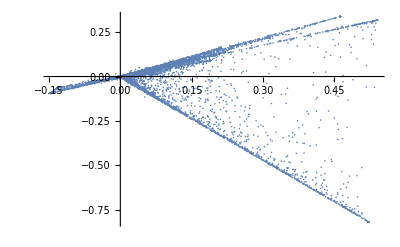

```mathematica
ListPlot[DimensionReduce[normalizedCellSpeciesMat,2],PlotRange->All]
```

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellDR*200)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellDR*1000)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellDR*200)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

#### Presence absence

```mathematica
cellPRDR=DimensionReduce[Unitize@cellSpeciesMat,3];
```

```mathematica
ListPointPlot3D[cellPRDR]
```

-Graphics3D-

```mathematica
ListPointPlot3D[cellPRDR,PlotRange->{{-1,1}*0.01,{-1,1}*0.01,Automatic}]
```

-Graphics3D-

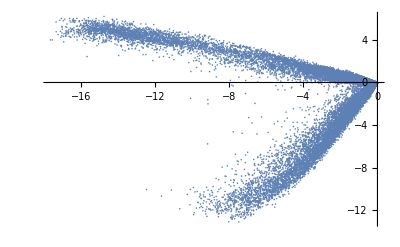

```mathematica
ListPlot[DimensionReduce[Unitize@cellSpeciesMat,2],PlotRange->All]
```

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellPRDR*1)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellPRDR*0.1)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

#### Presence absence with higher threshold

```mathematica
cellPRDR2=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]],3];
```

```mathematica
cellPRDR2=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]],3,Method->"TSNE"];//EchoTiming
```

5007.31

```mathematica
cellPRDR2=;
```

```mathematica
ListPointPlot3D[cellPRDR2]
```

-Graphics3D-

```mathematica
ListPointPlot3D[cellPRDR2]
```

-Graphics3D-

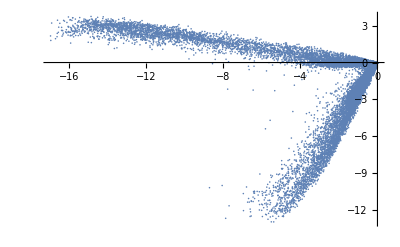

```mathematica
ListPlot[DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]],2],PlotRange->All]
```

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellPRDR2*1)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[Rescale[cellPRDR2],ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

t-SNE:

```mathematica
With[{ps=SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],Extract[(cellPRDR2*0.05)/2+0.5,ps]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

```mathematica
SparseArray[Total[cellSpeciesMat,{2}]]["NonzeroPositions"]
```

```mathematica
clusters=FindClusters[normalizedCellSpeciesMat,Method->"DBSCAN"];
```

### Regional dimension reduction

```mathematica
rmf=RegionMember[GeoGridPosition[Entity["Country","UnitedStates"]["Polygon"],"Equirectangular"]]
```

RegionMemberFunction[Polygon[GeoGridPosition[{{{-122.758, 49.0021}, {-121.758, 49.002}, {-120.758, 49.0019}, {-119.758, 49.0019}, {-118.758, 49.0018}, {-117.758, 49.0017}, {-116.758, 49.0016}, {-115.758, 49.0015}, {-114.758, 49.0015}, <<2646>>, {-122.793, 48.8925}, {-122.747, 48.9323}, {-122.822, 48.9421}, {-122.733, 48.9621}, {-122.758, 49.002}}, <<5>>}, Equi<<9>>ar]], <>]

```mathematica
regionPositions=Position[rmf[First@GeoGridPosition[cellPoints,"Equirectangular"]],True];
```

```mathematica
normalizedCellSpeciesMat[[regionPositions[[All,1]]]]
```

SparseArray[<443441>, {1555, 10478}]

```mathematica
cellDRUSA=DimensionReduce[normalizedCellSpeciesMat[[regionPositions[[All,1]]]],3];
```

```mathematica
cellDRUSA=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]],3,Method->"LatentSemanticAnalysis"];
```

```mathematica
cellDRUSA=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]],3,Method->"TSNE"];
```

```mathematica
cellDRUSA=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]],3,Method->"PrincipalComponentsAnalysis"];
```

```mathematica
cellDRUSA=DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]],3,Method->"Autoencoder",TargetDevice->"GPU"];
```

```mathematica
ListPointPlot3D[cellDRUSA]
```

-Graphics3D-

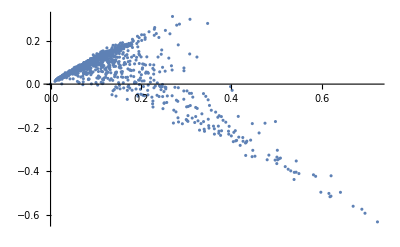

```mathematica
ListPlot[DimensionReduce[normalizedCellSpeciesMat[[regionPositions[[All,1]]]],2],PlotRange->All]
```

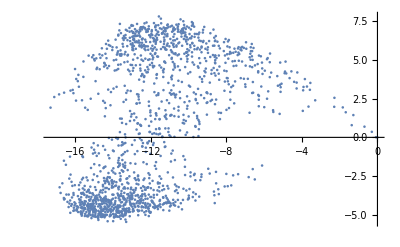

```mathematica
ListPlot[DimensionReduce[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]],2],PlotRange->All]
```

```mathematica
With[{ps=regionPositions},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],(cellDRUSA*0.03)/2+0.5}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

### Regional clustering

```mathematica
clusters=FindClusters[Unitize[Ramp[cellSpeciesMat-10]][[regionPositions[[All,1]]]]->Range[Length[regionPositions]],4,Method->"KMeans"];
```

```mathematica
With[{ps=regionPositions,indexClusters=Association@Catenate@MapIndexed[Thread[#1->First[#2]]&,clusters,{2}]},
GeoGraphics[{
GeoStyling[Opacity[1]],
MapThread[
Style[#1,RGBColor[#2]]&,
{Extract[cellPolygons,ps],ColorData[112]/@Lookup[indexClusters,Range[Length[ps]]]}
]
},GeoProjection->"WinkelTripel"]
]
```

-Graphics-

## Notes

Use other DR methods

Run clustering